```mathematica
<<IGraphM`
```

IGraph/M 0.4 (April 2, 2020)
Evaluate IGDocumentation[] to get started.

Hamming graph H(d, q). Vertex set is {0,1,...,q-1}^d. Edges are between vertices with exactly h different entries. By default, h = 1.

```mathematica
HammingGraph[d_,q_,h_Integer:1,opts:OptionsPattern[]]:=With[{v=Tuples[Range[0,q-1],d]},Graph[v,TwoWayRule@@@Select[Subsets[v,{2}],HammingDistance@@#==h&],opts]]
```

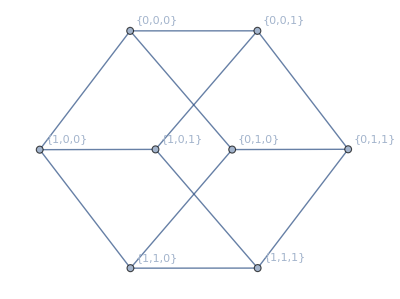

```mathematica
HammingGraph[3,2,VertexLabels->Automatic]
```

Fast algorithm which gives list of spectrums of a graph G over all possible signatures. 95% sure this works. I think runs in O((|V|)^3 2^(|E|-|V|)) before sorting.

```mathematica
SignedSpectrums[g_]:=Block[{m,f},
m=EdgeCycleMatrix[g];
f=Quiet@LinearSolve[m,Modulus->2];
If[Length[m]==0,{NumericalSort@Eigenvalues@AdjacencyMatrix[g]},
Sort@DeleteDuplicates@Append[NumericalSort@Eigenvalues@WeightedAdjacencyMatrix@Annotate[g,EdgeWeight->#]&/@Inner[#2->-2Mod[#1,2]+1&,Total/@Rest@Subsets[f/@IdentityMatrix@Length[m]],EdgeList[g],List],NumericalSort@Eigenvalues@AdjacencyMatrix[g]]]
]
```

Examples

```mathematica
SignedSpectrums[PetersenGraph[]]
```

{{-3,-1,-1,-1,-1,-1,2,2,2,2},{-2,-2,-2,-2,1,1,1,1,1,3},{-√5,-√5,-√5,0,0,0,0,√5,√5,√5},{1/2 (-1-√17),-√5,1/2 (1-√17),-1,0,0,1,1/2 (-1+√17),√5,1/2 (1+√17)},{Root-2.49Root[-2-7 #1+#1^3&,1]-2.4892885718100786,-2,-2,-1,Root-0.289Root[-2-7 #1+#1^3&,2]-0.28916854644830997,1,1,1,2,Root2.78Root[-2-7 #1+#1^3&,3]2.778457118258389},{Root-2.78Root[2-7 #1+#1^3&,1]-2.778457118258389,-2,-1,-1,-1,Root0.289Root[2-7 #1+#1^3&,2]0.28916854644830997,1,2,2,Root2.49Root[2-7 #1+#1^3&,3]2.4892885718100786}}

```mathematica
SignedSpectrums[HammingGraph[1,1]]
```

{{0}}

```mathematica
SignedSpectrums[HammingGraph[1,2]]
```

{{-1,1}}

```mathematica
SignedSpectrums[HammingGraph[1,3]]
```

{{-2,1,1},{-1,-1,2}}

```mathematica
SignedSpectrums[HammingGraph[1,4]]
```

{{-3,1,1,1},{-1,-1,-1,3},{-√5,-1,1,√5}}

```mathematica
SignedSpectrums[HammingGraph[1,5]]
```

{{-4,1,1,1,1},{-3,1/2 (1-√17),1,1,1/2 (1+√17)},{-1,-1,-1,-1,4},{-√5,-√5,0,√5,√5},{1/2 (-1-√17),-1,-1,1/2 (-1+√17),3},{1/2 (-1-√33),-1,1,1,1/2 (-1+√33)},{1/2 (1-√33),-1,-1,1,1/2 (1+√33)}}

```mathematica
SignedSpectrums[HammingGraph[1,6]]
```

{{-5,1,1,1,1,1},{-3,-3,1,1,1,3},{-3,-1,-1,-1,3,3},{-3,-√5,-1,1,√5,3},{-3,1-2 √2,-1,1,1,1+2 √2},{-1,-1,-1,-1,-1,5},{-√5,-√5,-√5,√5,√5,√5},{-√13,-1,-1,1,1,√13},{-1-2 √2,-1,-1,1,-1+2 √2,3},{-1-2 √3,-1,1,1,1,-1+2 √3},{1-2 √3,-1,-1,-1,1,1+2 √3},{-√(7+2 √5),-√(7-2 √5),-1,1,√(7-2 √5),√(7+2 √5)},{Root-2.76Root[19-9 #1-3 #1^2+#1^3&,1]-2.7587704831436337,-1,-1,-1,Root1.69Root[19-9 #1-3 #1^2+#1^3&,2]1.6945927106677214,Root4.06Root[19-9 #1-3 #1^2+#1^3&,3]4.0641777724759125},{Root-2.60Root[1-9 #1-#1^2+#1^3&,1]-2.6038754716096766,-√5,-1,Root0.110Root[1-9 #1-#1^2+#1^3&,2]0.10991626417474239,√5,Root3.49Root[1-9 #1-#1^2+#1^3&,3]3.493959207434934},{Root-3.49Root[-1-9 #1+#1^2+#1^3&,1]-3.493959207434934,-√5,Root-0.110Root[-1-9 #1+#1^2+#1^3&,2]-0.10991626417474239,1,√5,Root2.60Root[-1-9 #1+#1^2+#1^3&,3]2.6038754716096766},{Root-4.06Root[-19-9 #1+3 #1^2+#1^3&,1]-4.0641777724759125,Root-1.69Root[-19-9 #1+3 #1^2+#1^3&,2]-1.6945927106677214,1,1,1,Root2.76Root[-19-9 #1+3 #1^2+#1^3&,3]2.7587704831436337}}

```mathematica
SignedSpectrums[HammingGraph[1,7]]
```

{{-6,1,1,1,1,1,1},{-5,-2,1,1,1,1,3},{-5,-1,-1,1,1,2,3},{-3,-3,-2,1,1,3,3},{-3,-3,-1,-1,2,3,3},{-3,-3,1/2 (3-√33),1,1,1,1/2 (3+√33)},{-3,-2,-1,-1,1,1,5},{-3,-1,-1,-1,-1,2,5},{-3,-√5,-√5,1/2 (3-√17),√5,√5,1/2 (3+√17)},{-3,Root-2.49Root[-2-7 #1+#1^3&,1]-2.4892885718100786,1-2 √2,Root-0.289Root[-2-7 #1+#1^3&,2]-0.28916854644830997,1,Root2.78Root[-2-7 #1+#1^3&,3]2.778457118258389,1+2 √2},{-3,Root-2.59Root[26-7 #1-4 #1^2+#1^3&,1]-2.5877414504720115,-1,-1,1,Root2.40Root[26-7 #1-4 #1^2+#1^3&,2]2.398207430136929,Root4.19Root[26-7 #1-4 #1^2+#1^3&,3]4.189534020335082},{-3,Root-2.30Root[2-9 #1-2 #1^2+#1^3&,1]-2.2970705443632746,-1,-1,Root0.213Root[2-9 #1-2 #1^2+#1^3&,2]0.21319818492766704,3,Root4.08Root[2-9 #1-2 #1^2+#1^3&,3]4.083872359435608},{-1,-1,-1,-1,-1,-1,6},{-√17,-2,-1,1,1,1,√17},{-√17,-1,-1,-1,1,2,√17},{-1-2 √2,Root-2.78Root[2-7 #1+#1^3&,1]-2.778457118258389,-1,Root0.289Root[2-7 #1+#1^3&,2]0.28916854644830997,-1+2 √2,Root2.49Root[2-7 #1+#1^3&,3]2.4892885718100786,3},{-1-2 √2,Root-1.63Root[10-3 #1-4 #1^2+#1^3&,1]-1.6261980685272936,-1,-1,Root1.48Root[10-3 #1-4 #1^2+#1^3&,2]1.4848619528719296,-1+2 √2,Root4.14Root[10-3 #1-4 #1^2+#1^3&,3]4.141336115655364},{-1-2 √3,Root-2.49Root[-2-7 #1+#1^3&,1]-2.4892885718100786,Root-0.289Root[-2-7 #1+#1^3&,2]-0.28916854644830997,1,1,-1+2 √3,Root2.78Root[-2-7 #1+#1^3&,3]2.778457118258389},{1/2 (-3-√17),-√5,-√5,1/2 (-3+√17),√5,√5,3},{1/2 (-3-√33),-1,-1,-1,1/2 (-3+√33),3,3},{1/2 (-1-√41),-√5,-√5,1,√5,√5,1/2 (-1+√41)},{1/2 (1-√41),-√5,-√5,-1,√5,√5,1/2 (1+√41)},{1/2 (-1-√57),-3,1,1,1,1,1/2 (-1+√57)},{1/2 (1-√57),-1,-1,-1,-1,3,1/2 (1+√57)},{1/2 (-3-√65),-1,1,1,1,1,1/2 (-3+√65)},{1/2 (3-√65),-1,-1,-1,-1,1,1/2 (3+√65)},{1/2 (-1-√73),-1,-1,1,1,1,1/2 (-1+√73)},{1/2 (1-√73),-1,-1,-1,1,1,1/2 (1+√73)},{Root-2.78Root[2-7 #1+#1^3&,1]-2.778457118258389,1-2 √3,-1,-1,Root0.289Root[2-7 #1+#1^3&,2]0.28916854644830997,Root2.49Root[2-7 #1+#1^3&,3]2.4892885718100786,1+2 √3},{Root-2.90Root[26-11 #1-4 #1^2+#1^3&,1]-2.896549528131922,-1,-1,-1,-1,Root1.74Root[26-11 #1-4 #1^2+#1^3&,2]1.7411129184739242,Root5.16Root[26-11 #1-4 #1^2+#1^3&,3]5.155436609657998},{Root-2.83Root[2-13 #1-2 #1^2+#1^3&,1]-2.8347780391647914,-√5,-1,-1,Root0.151Root[2-13 #1-2 #1^2+#1^3&,2]0.15061883662670567,√5,Root4.68Root[2-13 #1-2 #1^2+#1^3&,3]4.684159202538086},{Root-3.39Root[18-13 #1-2 #1^2+#1^3&,1]-3.393636799197555,-√5,-1,-1,Root1.29Root[18-13 #1-2 #1^2+#1^3&,2]1.293684351422491,√5,Root4.10Root[18-13 #1-2 #1^2+#1^3&,3]4.099952447775064},{Root-3.50Root[22-13 #1-2 #1^2+#1^3&,1]-3.5033076346549765,-3,-1,1,1,Root1.62Root[22-13 #1-2 #1^2+#1^3&,2]1.6150716258115652,Root3.89Root[22-13 #1-2 #1^2+#1^3&,3]3.8882360088434114},{Root-2.60Root[1-9 #1-#1^2+#1^3&,1]-2.6038754716096766,Root-2.60Root[1-9 #1-#1^2+#1^3&,1]-2.6038754716096766,-2,Root0.110Root[1-9 #1-#1^2+#1^3&,2]0.10991626417474239,Root0.110Root[1-9 #1-#1^2+#1^3&,2]0.10991626417474239,Root3.49Root[1-9 #1-#1^2+#1^3&,3]3.493959207434934,Root3.49Root[1-9 #1-#1^2+#1^3&,3]3.493959207434934},{Root-3.49Root[-1-9 #1+#1^2+#1^3&,1]-3.493959207434934,Root-3.49Root[-1-9 #1+#1^2+#1^3&,1]-3.493959207434934,Root-0.110Root[-1-9 #1+#1^2+#1^3&,2]-0.10991626417474239,Root-0.110Root[-1-9 #1+#1^2+#1^3&,2]-0.10991626417474239,2,Root2.60Root[-1-9 #1+#1^2+#1^3&,3]2.6038754716096766,Root2.60Root[-1-9 #1+#1^2+#1^3&,3]2.6038754716096766},{Root-3.49Root[-1-9 #1+#1^2+#1^3&,1]-3.493959207434934,Root-2.44Root[18+#1-11 #1^2-#1^3+#1^4&,1]-2.4379957859484502,Root-1.51Root[18+#1-11 #1^2-#1^3+#1^4&,2]-1.513733706995218,Root-0.110Root[-1-9 #1+#1^2+#1^3&,2]-0.10991626417474239,Root1.36Root[18+#1-11 #1^2-#1^3+#1^4&,3]1.3567190172747754,Root2.60Root[-1-9 #1+#1^2+#1^3&,3]2.6038754716096766,Root3.60Root[18+#1-11 #1^2-#1^3+#1^4&,4]3.595010475668893},{Root-3.89Root[-22-13 #1+2 #1^2+#1^3&,1]-3.8882360088434114,Root-1.62Root[-22-13 #1+2 #1^2+#1^3&,2]-1.6150716258115652,-1,-1,1,3,Root3.50Root[-22-13 #1+2 #1^2+#1^3&,3]3.5033076346549765},{Root-4.10Root[-18-13 #1+2 #1^2+#1^3&,1]-4.099952447775064,-√5,Root-1.29Root[-18-13 #1+2 #1^2+#1^3&,2]-1.293684351422491,1,1,√5,Root3.39Root[-18-13 #1+2 #1^2+#1^3&,3]3.393636799197555},{Root-4.68Root[-2-13 #1+2 #1^2+#1^3&,1]-4.684159202538086,-√5,Root-0.151Root[-2-13 #1+2 #1^2+#1^3&,2]-0.15061883662670567,1,1,√5,Root2.83Root[-2-13 #1+2 #1^2+#1^3&,3]2.8347780391647914},{Root-4.08Root[-2-9 #1+2 #1^2+#1^3&,1]-4.083872359435608,-3,Root-0.213Root[-2-9 #1+2 #1^2+#1^3&,2]-0.21319818492766704,1,1,Root2.30Root[-2-9 #1+2 #1^2+#1^3&,3]2.2970705443632746,3},{Root-5.16Root[-26-11 #1+4 #1^2+#1^3&,1]-5.155436609657998,Root-1.74Root[-26-11 #1+4 #1^2+#1^3&,2]-1.7411129184739242,1,1,1,1,Root2.90Root[-26-11 #1+4 #1^2+#1^3&,3]2.896549528131922},{Root-4.19Root[-26-7 #1+4 #1^2+#1^3&,1]-4.189534020335082,Root-2.40Root[-26-7 #1+4 #1^2+#1^3&,2]-2.398207430136929,-1,1,1,Root2.59Root[-26-7 #1+4 #1^2+#1^3&,3]2.5877414504720115,3},{Root-4.14Root[-10-3 #1+4 #1^2+#1^3&,1]-4.141336115655364,1-2 √2,Root-1.48Root[-10-3 #1+4 #1^2+#1^3&,2]-1.4848619528719296,1,1,Root1.63Root[-10-3 #1+4 #1^2+#1^3&,3]1.6261980685272936,1+2 √2},{Root-3.40Root[50+#1-19 #1^2-#1^3+#1^4&,1]-3.401657054688848,Root-1.88Root[50+#1-19 #1^2-#1^3+#1^4&,2]-1.8829247934381055,-1,-1,1,Root1.70Root[50+#1-19 #1^2-#1^3+#1^4&,3]1.704351599606727,Root4.58Root[50+#1-19 #1^2-#1^3+#1^4&,4]4.580230248520226},{Root-3.64Root[46+5 #1-19 #1^2-#1^3+#1^4&,1]-3.641810122653553,Root-1.60Root[46+5 #1-19 #1^2-#1^3+#1^4&,2]-1.6002300187239806,-1,-1,1,Root1.76Root[46+5 #1-19 #1^2-#1^3+#1^4&,3]1.7618014800219588,Root4.48Root[46+5 #1-19 #1^2-#1^3+#1^4&,4]4.480238661355575},{Root-3.53Root[34+13 #1-15 #1^2-#1^3+#1^4&,1]-3.5251375136823184,-3,Root-1.22Root[34+13 #1-15 #1^2-#1^3+#1^4&,2]-1.2159109486747621,1,1,Root2.32Root[34+13 #1-15 #1^2-#1^3+#1^4&,3]2.31593097889531,Root3.43Root[34+13 #1-15 #1^2-#1^3+#1^4&,4]3.425117483461771},{Root-4.01Root[2+21 #1-15 #1^2-#1^3+#1^4&,1]-4.012185037025408,-√5,-1,Root-0.0895Root[2+21 #1-15 #1^2-#1^3+#1^4&,2]-0.08954764956046499,Root1.58Root[2+21 #1-15 #1^2-#1^3+#1^4&,3]1.5811977802162884,√5,Root3.52Root[2+21 #1-15 #1^2-#1^3+#1^4&,4]3.5205349063695848},{Root-4.48Root[46-5 #1-19 #1^2+#1^3+#1^4&,1]-4.480238661355575,Root-1.76Root[46-5 #1-19 #1^2+#1^3+#1^4&,2]-1.7618014800219588,-1,1,1,Root1.60Root[46-5 #1-19 #1^2+#1^3+#1^4&,3]1.6002300187239806,Root3.64Root[46-5 #1-19 #1^2+#1^3+#1^4&,4]3.641810122653553},{Root-4.58Root[50-#1-19 #1^2+#1^3+#1^4&,1]-4.580230248520226,Root-1.70Root[50-#1-19 #1^2+#1^3+#1^4&,2]-1.704351599606727,-1,1,1,Root1.88Root[50-#1-19 #1^2+#1^3+#1^4&,3]1.8829247934381055,Root3.40Root[50-#1-19 #1^2+#1^3+#1^4&,4]3.401657054688848},{Root-3.52Root[2-21 #1-15 #1^2+#1^3+#1^4&,1]-3.5205349063695848,-√5,Root-1.58Root[2-21 #1-15 #1^2+#1^3+#1^4&,2]-1.5811977802162884,Root0.0895Root[2-21 #1-15 #1^2+#1^3+#1^4&,3]0.08954764956046499,1,√5,Root4.01Root[2-21 #1-15 #1^2+#1^3+#1^4&,4]4.012185037025408},{Root-3.43Root[34-13 #1-15 #1^2+#1^3+#1^4&,1]-3.425117483461771,Root-2.32Root[34-13 #1-15 #1^2+#1^3+#1^4&,2]-2.31593097889531,-1,-1,Root1.22Root[34-13 #1-15 #1^2+#1^3+#1^4&,3]1.2159109486747621,3,Root3.53Root[34-13 #1-15 #1^2+#1^3+#1^4&,4]3.5251375136823184},{Root-3.60Root[18-#1-11 #1^2+#1^3+#1^4&,1]-3.595010475668893,Root-2.60Root[1-9 #1-#1^2+#1^3&,1]-2.6038754716096766,Root-1.36Root[18-#1-11 #1^2+#1^3+#1^4&,2]-1.3567190172747754,Root0.110Root[1-9 #1-#1^2+#1^3&,2]0.10991626417474239,Root1.51Root[18-#1-11 #1^2+#1^3+#1^4&,3]1.513733706995218,Root2.44Root[18-#1-11 #1^2+#1^3+#1^4&,4]2.4379957859484502,Root3.49Root[1-9 #1-#1^2+#1^3&,3]3.493959207434934},{Root-3.63Root[2+83 #1-2 #1^2-20 #1^3+#1^5&,1]-3.6340862182698435,Root-2.54Root[2+83 #1-2 #1^2-20 #1^3+#1^5&,2]-2.5365609484910823,-1,Root-0.0241Root[2+83 #1-2 #1^2-20 #1^3+#1^5&,3]-0.02408577346825096,1,Root2.33Root[2+83 #1-2 #1^2-20 #1^3+#1^5&,4]2.332076431009337,Root3.86Root[2+83 #1-2 #1^2-20 #1^3+#1^5&,5]3.8626565092198395},{Root-3.86Root[-2+83 #1+2 #1^2-20 #1^3+#1^5&,1]-3.8626565092198395,Root-2.33Root[-2+83 #1+2 #1^2-20 #1^3+#1^5&,2]-2.332076431009337,-1,Root0.0241Root[-2+83 #1+2 #1^2-20 #1^3+#1^5&,3]0.02408577346825096,1,Root2.54Root[-2+83 #1+2 #1^2-20 #1^3+#1^5&,4]2.5365609484910823,Root3.63Root[-2+83 #1+2 #1^2-20 #1^3+#1^5&,5]3.6340862182698435}}

```mathematica
SignedSpectrums[HammingGraph[2,1]]
```

{{0}}

```mathematica
SignedSpectrums[HammingGraph[2,2]]
```

{{-2,0,0,2},{-√2,-√2,√2,√2}}

```mathematica
SignedSpectrums[HammingGraph[2,3]]
```

{{-4,-1,-1,-1,-1,2,2,2,2},{-3,-3,-2,0,1,1,2,2,2},{-3,-3,0,0,0,0,0,3,3},{-3,-2,-2,1/2 (1-√17),1,1,2,2,1/2 (1+√17)},{-3,-2,-2,1/2 (3-√17),0,1,1,2,1/2 (3+√17)},{-3,1/2 (-1-√17),1/2 (1-√17),0,0,0,1/2 (-1+√17),1/2 (1+√17),3},{-3,1/2 (1-√17),1/2 (1-√17),1/2 (1-√17),0,0,1/2 (1+√17),1/2 (1+√17),1/2 (1+√17)},{-3,1/2 (1-√33),1/2 (1-√17),0,0,0,1,1/2 (1+√17),1/2 (1+√33)},{-3,Root-2.86Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,1]-2.8643479250586186,Root-1.35Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,2]-1.3535666163796758,Root-0.423Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,3]-0.4230724946411308,0,1,Root1.61Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,4]1.6081039795902952,2,Root3.03Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,5]3.03288305648913},{-2,-2,-2,-2,1,1,1,1,4},{-2,-2,-2,-1,-1,0,2,3,3},{-2,-2,-2,1/2 (1-√17),1/2 (3-√17),1,1,1/2 (1+√17),1/2 (3+√17)},{-2 √2,-√5,-√5,0,0,0,√5,√5,2 √2},{1/2 (-3-√17),-2,-1,-1,0,1/2 (-3+√17),2,2,3},{1/2 (-3-√17),1/2 (-1-√17),-1,-1,1/2 (-3+√17),1/2 (-1+√17),2,2,2},{1/2 (-1-√17),-2,-2,-1,-1,1/2 (-1+√17),2,2,3},{1/2 (-1-√17),1/2 (-1-√17),1/2 (-1-√17),0,0,1/2 (-1+√17),1/2 (-1+√17),1/2 (-1+√17),3},{1/2 (-1-√17),1/2 (-1-√17),1/2 (1-√17),1/2 (1-√17),0,1/2 (-1+√17),1/2 (-1+√17),1/2 (1+√17),1/2 (1+√17)},{1/2 (-1-√33),-2,-2,-1,1,1,2,2,1/2 (-1+√33)},{1/2 (-1-√33),1/2 (-1-√17),-1,0,0,0,1/2 (-1+√17),1/2 (-1+√33),3},{1/2 (1-√33),-2,-2,-1,-1,1,2,2,1/2 (1+√33)},{-√(1/2 (9+√33)),-2,Root-1.68Root[2-5 #1-2 #1^2+#1^3&,1]-1.6813306436049773,-√(1/2 (9-√33)),0,Root0.358Root[2-5 #1-2 #1^2+#1^3&,2]0.35792636751849977,√(1/2 (9-√33)),√(1/2 (9+√33)),Root3.32Root[2-5 #1-2 #1^2+#1^3&,3]3.3234042760864777},{1/2 (-1-√41),-2,-1,-1,0,1,2,2,1/2 (-1+√41)},{1/2 (1-√41),-2,-2,-1,0,1,1,2,1/2 (1+√41)},{-√(1/2 (13+√73)),-√5,-√(1/2 (13-√73)),0,0,0,√(1/2 (13-√73)),√5,√(1/2 (13+√73))},{-√(Root9.90Root[-96+80 #1-17 #1^2+#1^3&,3]9.896549528131922),-√(Root5.26Root[-96+80 #1-17 #1^2+#1^3&,2]5.258887081526075),-√(Root1.84Root[-96+80 #1-17 #1^2+#1^3&,1]1.844563390342002),-1,0,1,√(Root1.84Root[-96+80 #1-17 #1^2+#1^3&,1]1.844563390342002),√(Root5.26Root[-96+80 #1-17 #1^2+#1^3&,2]5.258887081526075),√(Root9.90Root[-96+80 #1-17 #1^2+#1^3&,3]9.896549528131922)},{-√(Root8.92Root[-32+40 #1-13 #1^2+#1^3&,3]8.916381551744971),-√5,-√(Root2.80Root[-32+40 #1-13 #1^2+#1^3&,2]2.8034424062557384),-√(Root1.28Root[-32+40 #1-13 #1^2+#1^3&,1]1.28017604199929),0,√(Root1.28Root[-32+40 #1-13 #1^2+#1^3&,1]1.28017604199929),√(Root2.80Root[-32+40 #1-13 #1^2+#1^3&,2]2.8034424062557384),√5,√(Root8.92Root[-32+40 #1-13 #1^2+#1^3&,3]8.916381551744971)},{Root-3.08Root[8-10 #1-#1^2+#1^3&,1]-3.0838723594356074,-2,-1,-1,-1,Root0.787Root[8-10 #1-#1^2+#1^3&,2]0.7868018150723329,2,2,Root3.30Root[8-10 #1-#1^2+#1^3&,3]3.2970705443632746},{Root-2.63Root[4-8 #1-#1^2+#1^3&,1]-2.6261980685272936,-2,1/2 (1-√17),-1,-1,Root0.485Root[4-8 #1-#1^2+#1^3&,2]0.48486195287192946,2,1/2 (1+√17),Root3.14Root[4-8 #1-#1^2+#1^3&,3]3.1413361156553643},{Root-3.30Root[-8-10 #1+#1^2+#1^3&,1]-3.2970705443632746,-2,-2,Root-0.787Root[-8-10 #1+#1^2+#1^3&,2]-0.7868018150723329,1,1,1,2,Root3.08Root[-8-10 #1+#1^2+#1^3&,3]3.0838723594356074},{Root-3.14Root[-4-8 #1+#1^2+#1^3&,1]-3.1413361156553643,1/2 (-1-√17),-2,Root-0.485Root[-4-8 #1+#1^2+#1^3&,2]-0.48486195287192946,1,1,1/2 (-1+√17),2,Root2.63Root[-4-8 #1+#1^2+#1^3&,3]2.6261980685272936},{Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777,-√(1/2 (9+√33)),-√(1/2 (9-√33)),Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977,0,√(1/2 (9-√33)),Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773,2,√(1/2 (9+√33))},{Root-2.92Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,1]-2.9180712601895626,1/2 (-1-√17),Root-1.71Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,2]-1.7113570185398204,Root-0.523Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,3]-0.5226322900564215,0,1,1/2 (-1+√17),Root1.87Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,4]1.8650068274233664,Root3.29Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,5]3.2870537413624383},{Root-3.29Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,1]-3.2870537413624383,Root-1.87Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,2]-1.8650068274233664,1/2 (1-√17),-1,0,Root0.523Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,3]0.5226322900564215,Root1.71Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,4]1.7113570185398204,1/2 (1+√17),Root2.92Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,5]2.9180712601895626},{Root-2.86Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,1]-2.8643479250586186,-2,1/2 (1-√17),Root-1.35Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,2]-1.3535666163796758,Root-0.423Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,3]-0.4230724946411308,1,Root1.61Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,4]1.6081039795902952,1/2 (1+√17),Root3.03Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,5]3.03288305648913},{Root-3.03Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,1]-3.03288305648913,-2,Root-1.61Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,2]-1.6081039795902952,-1,0,Root0.423Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,3]0.4230724946411308,Root1.35Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,4]1.3535666163796758,Root2.86Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,5]2.8643479250586186,3},{Root-3.03Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,1]-3.03288305648913,1/2 (-1-√17),Root-1.61Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,2]-1.6081039795902952,-1,Root0.423Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,3]0.4230724946411308,Root1.35Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,4]1.3535666163796758,1/2 (-1+√17),2,Root2.86Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,5]2.8643479250586186},{Root-2.72Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,1]-2.720776369811733,1/2 (-1-√17),Root-1.43Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,2]-1.4250608296658274,-1,0,Root0.547Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,3]0.547490075346859,1/2 (-1+√17),Root2.25Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,4]2.253239988499998,Root3.35Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,5]3.3451071356307036},{Root-2.94Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,1]-2.937483210647963,-2,Root-1.84Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,2]-1.8395865694310856,-1,0,Root0.615Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,3]0.6148206737172228,Root1.78Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,4]1.7796567553770106,2,Root3.38Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,5]3.382592350984815},{Root-3.38Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,1]-3.382592350984815,-2,Root-1.78Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,2]-1.7796567553770106,Root-0.615Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,3]-0.6148206737172228,0,1,Root1.84Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,4]1.8395865694310856,2,Root2.94Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,5]2.937483210647963},{Root-3.35Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,1]-3.3451071356307036,Root-2.25Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,2]-2.253239988499998,1/2 (1-√17),Root-0.547Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,3]-0.547490075346859,0,1,Root1.43Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,4]1.4250608296658274,1/2 (1+√17),Root2.72Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,5]2.720776369811733},{Root-2.98Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,1]-2.9780662751507307,1/2 (-1-√17),Root-1.92Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,2]-1.9240015070248142,Root-0.362Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,3]-0.3621066981013368,0,Root1.22Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,4]1.2229930580937294,1/2 (-1+√17),Root2.30Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,5]2.3017858720928506,Root2.74Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,6]2.739395550090302},{Root-2.74Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,1]-2.739395550090302,Root-2.30Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,2]-2.3017858720928506,1/2 (1-√17),Root-1.22Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,3]-1.2229930580937294,0,Root0.362Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,4]0.3621066981013368,Root1.92Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,5]1.9240015070248142,1/2 (1+√17),Root2.98Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,6]2.9780662751507307}}

```mathematica
SignedSpectrums[HammingGraph[3,1]]
```

{{0}}

```mathematica
SignedSpectrums[HammingGraph[3,2]]
```

{{-3,-1,-1,-1,1,1,1,3},{-√3,-√3,-√3,-√3,√3,√3,√3,√3},{-√5,-√5,-1,-1,1,1,√5,√5},{-1-√2,-√3,-√3,1-√2,-1+√2,√3,√3,1+√2},{-1-√2,-1-√2,1-√2,1-√2,-1+√2,-1+√2,1+√2,1+√2},{Root-2.71Root[-1-5 #1+#1^2+#1^3&,1]-2.7092753594369228,Root-1.90Root[1-5 #1-#1^2+#1^3&,1]-1.9032119259115532,-1,Root-0.194Root[-1-5 #1+#1^2+#1^3&,2]-0.19393656647463045,Root0.194Root[1-5 #1-#1^2+#1^3&,2]0.19393656647463045,1,Root1.90Root[-1-5 #1+#1^2+#1^3&,3]1.9032119259115532,Root2.71Root[1-5 #1-#1^2+#1^3&,3]2.7092753594369228}}

```mathematica
SignedSpectrums[HammingGraph[4,1]]
```

{{0}}

```mathematica
SignedSpectrums[HammingGraph[4,2]]
```

$Aborted

```mathematica
SelectSignedGraphs[g_Graph,test_Function]:=Block[{m,f},
m=EdgeCycleMatrix[g];
f=Quiet@LinearSolve[m,Modulus->2];
IGEdgeMap[If[#==1,Blue,Red]&,EdgeStyle->IGEdgeProp[EdgeWeight],#]&/@Select[Annotate[g,{EdgeWeight->#,VertexLabels->Automatic,EdgeStyle->Thick}]&/@Inner[#2->-2Mod[#1,2]+1&,Total/@Rest@Subsets[f/@IdentityMatrix@Length[m]],EdgeList[g],List],test@Sort@Eigenvalues@WeightedAdjacencyMatrix[#]&]
]
```

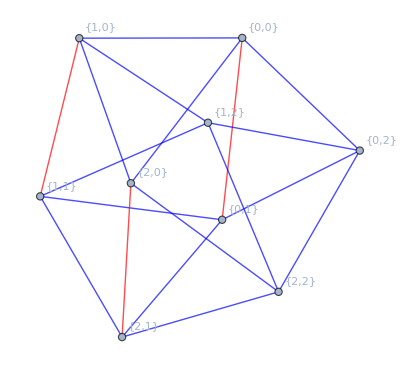
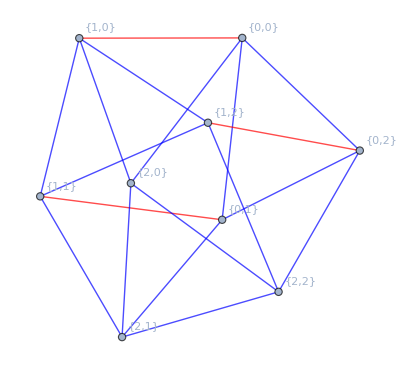

```mathematica
SelectSignedGraphs[HammingGraph[2,3],#==-Reverse[#]&]
```

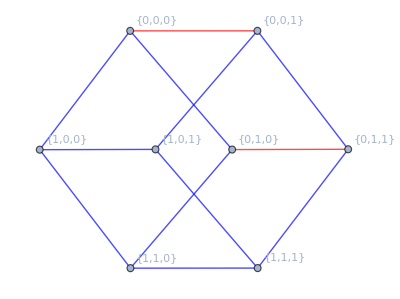
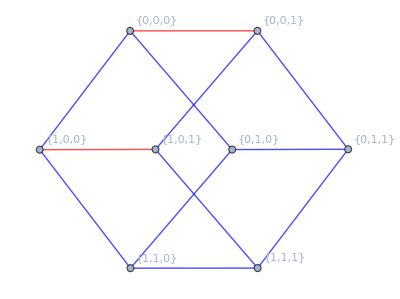
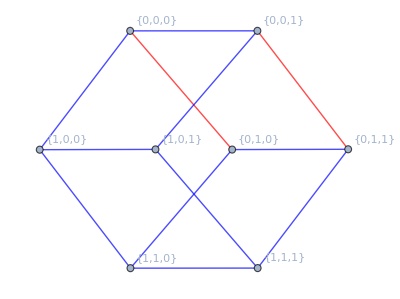
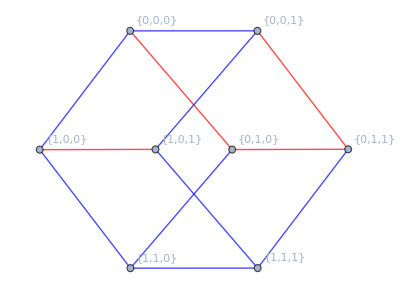

```mathematica
SelectSignedGraphs[HammingGraph[3,2],#==-Reverse[#]&]
```

```mathematica
SignedGraphs[g_]:=Block[{m,f},
m=EdgeCycleMatrix[g];
f=Quiet@LinearSolve[m,Modulus->2];
IGEdgeMap[If[#==1,Blue,Red]&,EdgeStyle->IGEdgeProp[EdgeWeight],#]&/@(Annotate[g,{EdgeWeight->#,VertexLabels->Automatic,EdgeStyle->Thick}]&/@Inner[#2->-2Mod[#1,2]+1&,Total/@Rest@Subsets[f/@IdentityMatrix@Length[m]],EdgeList[g],List])
]
```

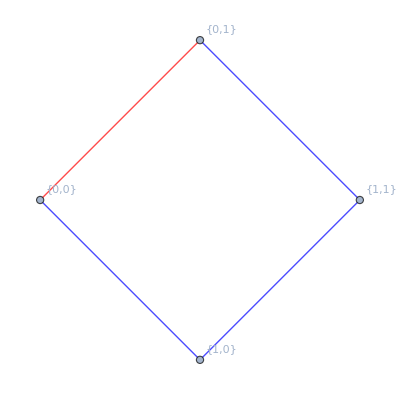

```mathematica
SignedGraphs[HammingGraph[2,2]]
```

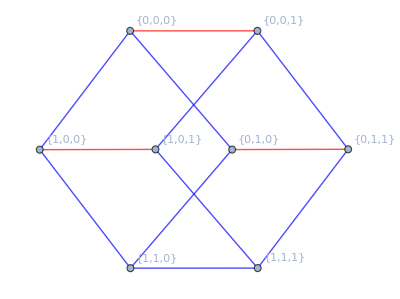
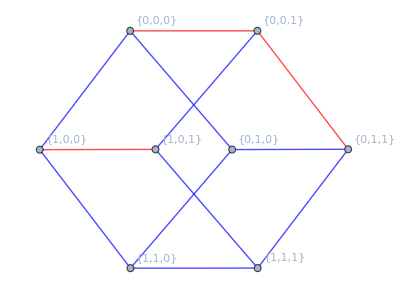
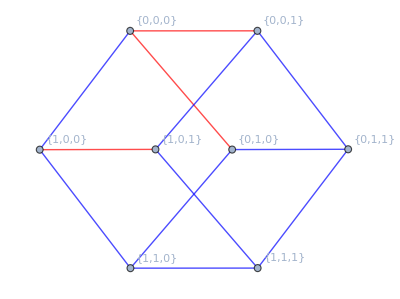
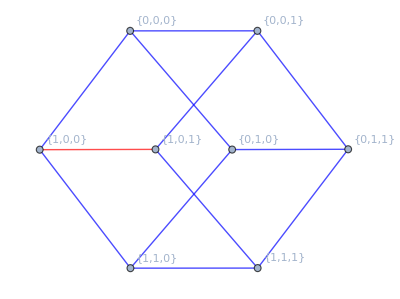
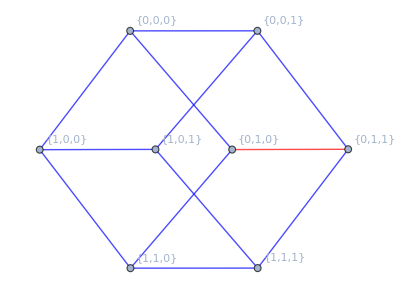
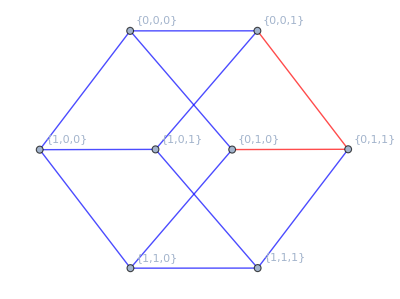
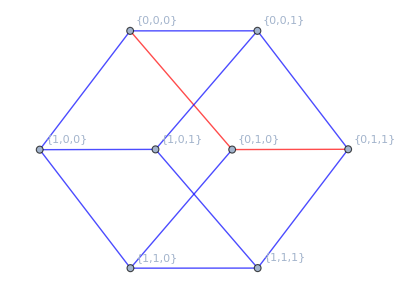
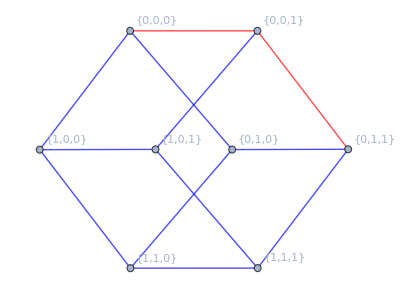
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SignedGraphs[HammingGraph[3,2]]
```

```mathematica
Through[{VertexCount,EdgeCount}[HammingGraph[4,2]]]
```

{16,32}

```mathematica
16^3*2^16
```

268435456

```mathematica
SignedGraphs[HammingGraph[4,2]]
```

$Aborted

```mathematica
Through[{VertexCount,EdgeCount}[HammingGraph[1,8]]]
```

{8,28}

```mathematica
8^3*2^20
```

536870912

```mathematica
Through[{VertexCount,EdgeCount}[HammingGraph[1,9]]]
```

{9,36}

```mathematica
9^3*2^(36-9)
```

97844723712

Lattice graph with n rows and m columns.

```mathematica
LatticeGraph[n_,m_]:=Graph[Flatten[Table[{i,j},{i,m},{j,n}],1],Join[Flatten[Table[{i,j}<->{i,k},{i,m},{j,n},{k,j+1,n}],2],Flatten[Table[{i,j}<->{k,j},{i,m},{j,n},{k,i+1,m}],2]]]
```

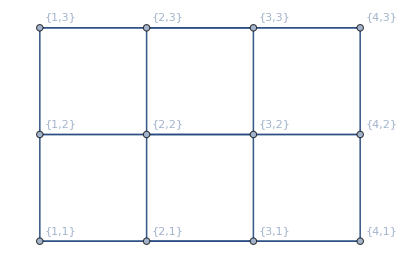

```mathematica
GraphPlot[LatticeGraph[3,4],GraphLayout->"GridEmbedding",VertexLabels->Automatic]
```

```mathematica
SignedSpectrums[LatticeGraph[2,2]]
```

{{-2,0,0,2},{-√2,-√2,√2,√2}}

```mathematica
SignedSpectrums[LatticeGraph[2,3]]
```

{{-3,-1,0,0,2,2},{-2,-2,0,0,1,3},{-2,1/2 (1-√17),-1,0,2,1/2 (1+√17)},{-√5,-√2,-√2,√2,√2,√5},{1/2 (-1-√17),-2,0,1,1/2 (-1+√17),2},{-√(1/2 (7+√41)),-√2,-√(1/2 (7-√41)),√(1/2 (7-√41)),√2,√(1/2 (7+√41))}}

```mathematica
SignedSpectrums[LatticeGraph[2,4]]
```

{{-4,-2,0,0,0,2,2,2},{-2,-2,-2,0,0,0,2,4},{-2,-2,1-√5,1-√5,0,0,1+√5,1+√5},{-2,-2,1-√7,1-√3,0,0,1+√3,1+√7},{-2 √2,-2,-2,0,0,2,2,2 √2},{-√6,-2,-√2,1-√5,0,√2,√6,1+√5},{-√6,-√6,-√2,-√2,√2,√2,√6,√6},{-√10,-√2,-√2,-√2,√2,√2,√2,√10},{-2-√2,-√2,-√2,-2+√2,2-√2,√2,√2,2+√2},{-√(2 (2+√2)),-√(2 (2+√2)),-√(2 (2-√2)),-√(2 (2-√2)),√(2 (2-√2)),√(2 (2-√2)),√(2 (2+√2)),√(2 (2+√2))},{-1-√3,-1-√3,1-√3,1-√3,-1+√3,-1+√3,1+√3,1+√3},{-1-√3,Root-2.25Root[8-6 #1-2 #1^2+#1^3&,1]-2.2491405381295495,-2,0,-1+√3,Root1.15Root[8-6 #1-2 #1^2+#1^3&,2]1.1463654890329085,2,Root3.10Root[8-6 #1-2 #1^2+#1^3&,3]3.102775049096641},{-1-√3,Root-2.61Root[4+12 #1-8 #1^2-2 #1^3+#1^4&,1]-2.6074690579861564,-√2,Root-0.284Root[4+12 #1-8 #1^2-2 #1^3+#1^4&,2]-0.2839417587785536,-1+√3,√2,Root1.68Root[4+12 #1-8 #1^2-2 #1^3+#1^4&,3]1.6849385912546877,Root3.21Root[4+12 #1-8 #1^2-2 #1^3+#1^4&,4]3.2064722255100224},{-1-√5,-2,1-√5,0,0,-1+√5,2,1+√5},{-1-√5,-√6,-√2,0,-1+√5,√2,2,√6},{-1-√5,-1-√5,0,0,-1+√5,-1+√5,2,2},{-√(5+√5),-√(3+√5),-√(5-√5),-√(3-√5),√(3-√5),√(5-√5),√(3+√5),√(5+√5)},{-1-√7,-1-√3,0,0,-1+√3,-1+√7,2,2},{-√(2 (3+√7)),-√2,-√2,-√(2 (3-√7)),√(2 (3-√7)),√2,√2,√(2 (3+√7))},{-√(5+√21),-√(3+√5),-√(3-√5),-√(5-√21),√(5-√21),√(3-√5),√(3+√5),√(5+√21)},{-√(2 (2+√(2+√2))),-√(2 (2+√(2-√2))),-√(2 (2-√(2-√2))),-√(2 (2-√(2+√2))),√(2 (2-√(2+√2))),√(2 (2-√(2-√2))),√(2 (2+√(2-√2))),√(2 (2+√(2+√2)))},{-√(Root8.69Root[-16+48 #1-14 #1^2+#1^3&,3]8.68584616555434),-√(Root4.94Root[-16+48 #1-14 #1^2+#1^3&,2]4.941366839742321),-√2,-√(Root0.373Root[-16+48 #1-14 #1^2+#1^3&,1]0.37278699470333837),√(Root0.373Root[-16+48 #1-14 #1^2+#1^3&,1]0.37278699470333837),√2,√(Root4.94Root[-16+48 #1-14 #1^2+#1^3&,2]4.941366839742321),√(Root8.69Root[-16+48 #1-14 #1^2+#1^3&,3]8.68584616555434)},{Root-3.10Root[-8-6 #1+2 #1^2+#1^3&,1]-3.102775049096641,-2,Root-1.15Root[-8-6 #1+2 #1^2+#1^3&,2]-1.1463654890329085,1-√3,0,2,Root2.25Root[-8-6 #1+2 #1^2+#1^3&,3]2.2491405381295495,1+√3},{Root-2.78Root[8+12 #1-10 #1^2-2 #1^3+#1^4&,1]-2.779163846875189,-2,-√2,Root-0.491Root[8+12 #1-10 #1^2-2 #1^3+#1^4&,2]-0.49060053808382426,0,√2,Root1.60Root[8+12 #1-10 #1^2-2 #1^3+#1^4&,3]1.59797547349208,Root3.67Root[8+12 #1-10 #1^2-2 #1^3+#1^4&,4]3.6717889114669333},{Root-3.67Root[8-12 #1-10 #1^2+2 #1^3+#1^4&,1]-3.6717889114669333,Root-1.60Root[8-12 #1-10 #1^2+2 #1^3+#1^4&,2]-1.59797547349208,-√2,0,Root0.491Root[8-12 #1-10 #1^2+2 #1^3+#1^4&,3]0.49060053808382426,√2,2,Root2.78Root[8-12 #1-10 #1^2+2 #1^3+#1^4&,4]2.779163846875189},{Root-3.21Root[4-12 #1-8 #1^2+2 #1^3+#1^4&,1]-3.2064722255100224,Root-1.68Root[4-12 #1-8 #1^2+2 #1^3+#1^4&,2]-1.6849385912546877,-√2,1-√3,Root0.284Root[4-12 #1-8 #1^2+2 #1^3+#1^4&,3]0.2839417587785536,√2,Root2.61Root[4-12 #1-8 #1^2+2 #1^3+#1^4&,4]2.6074690579861564,1+√3},{Root-2.79Root[-4-12 #1-6 #1^2+2 #1^3+#1^4&,1]-2.793604493334841,Root-1.83Root[4+4 #1-6 #1^2-2 #1^3+#1^4&,1]-1.8268383953119516,Root-1.28Root[-4-12 #1-6 #1^2+2 #1^3+#1^4&,2]-1.2840790438404124,Root-0.600Root[4+4 #1-6 #1^2-2 #1^3+#1^4&,2]-0.6001956935961277,Root-0.442Root[-4-12 #1-6 #1^2+2 #1^3+#1^4&,3]-0.4424634841649486,Root1.09Root[4+4 #1-6 #1^2-2 #1^3+#1^4&,3]1.0947875877430742,Root2.52Root[-4-12 #1-6 #1^2+2 #1^3+#1^4&,4]2.520147021340202,Root3.33Root[4+4 #1-6 #1^2-2 #1^3+#1^4&,4]3.332246501165005},{Root-3.33Root[4-4 #1-6 #1^2+2 #1^3+#1^4&,1]-3.332246501165005,Root-2.52Root[-4+12 #1-6 #1^2-2 #1^3+#1^4&,1]-2.520147021340202,Root-1.09Root[4-4 #1-6 #1^2+2 #1^3+#1^4&,2]-1.0947875877430742,Root0.442Root[-4+12 #1-6 #1^2-2 #1^3+#1^4&,2]0.4424634841649486,Root0.600Root[4-4 #1-6 #1^2+2 #1^3+#1^4&,3]0.6001956935961277,Root1.28Root[-4+12 #1-6 #1^2-2 #1^3+#1^4&,3]1.2840790438404124,Root1.83Root[4-4 #1-6 #1^2+2 #1^3+#1^4&,4]1.8268383953119516,Root2.79Root[-4+12 #1-6 #1^2-2 #1^3+#1^4&,4]2.793604493334841},{Root-2.70Root[8+48 #1+44 #1^2-8 #1^3-14 #1^4+#1^6&,1]-2.699780089384305,Root-1.70Root[8+48 #1+44 #1^2-8 #1^3-14 #1^4+#1^6&,2]-1.7037785021912804,-√2,Root-1.07Root[8+48 #1+44 #1^2-8 #1^3-14 #1^4+#1^6&,3]-1.0725660917684519,Root-0.207Root[8+48 #1+44 #1^2-8 #1^3-14 #1^4+#1^6&,4]-0.20681844808199107,√2,Root2.36Root[8+48 #1+44 #1^2-8 #1^3-14 #1^4+#1^6&,5]2.3581326187796616,Root3.32Root[8+48 #1+44 #1^2-8 #1^3-14 #1^4+#1^6&,6]3.3248105126463665},{Root-3.32Root[8-48 #1+44 #1^2+8 #1^3-14 #1^4+#1^6&,1]-3.3248105126463665,Root-2.36Root[8-48 #1+44 #1^2+8 #1^3-14 #1^4+#1^6&,2]-2.3581326187796616,-√2,Root0.207Root[8-48 #1+44 #1^2+8 #1^3-14 #1^4+#1^6&,3]0.20681844808199107,Root1.07Root[8-48 #1+44 #1^2+8 #1^3-14 #1^4+#1^6&,4]1.0725660917684519,√2,Root1.70Root[8-48 #1+44 #1^2+8 #1^3-14 #1^4+#1^6&,5]1.7037785021912804,Root2.70Root[8-48 #1+44 #1^2+8 #1^3-14 #1^4+#1^6&,6]2.699780089384305},{Root-2.76Root[-16-16 #1+32 #1^2+16 #1^3-12 #1^4-2 #1^5+#1^6&,1]-2.7556704964351937,-2,Root-1.34Root[-16-16 #1+32 #1^2+16 #1^3-12 #1^4-2 #1^5+#1^6&,2]-1.343371382254671,Root-0.589Root[-16-16 #1+32 #1^2+16 #1^3-12 #1^4-2 #1^5+#1^6&,3]-0.5891604546467262,0,Root0.931Root[-16-16 #1+32 #1^2+16 #1^3-12 #1^4-2 #1^5+#1^6&,4]0.9312635431047431,Root2.24Root[-16-16 #1+32 #1^2+16 #1^3-12 #1^4-2 #1^5+#1^6&,5]2.239681676408768,Root3.52Root[-16-16 #1+32 #1^2+16 #1^3-12 #1^4-2 #1^5+#1^6&,6]3.5172571138230797},{Root-3.52Root[-16+16 #1+32 #1^2-16 #1^3-12 #1^4+2 #1^5+#1^6&,1]-3.5172571138230797,Root-2.24Root[-16+16 #1+32 #1^2-16 #1^3-12 #1^4+2 #1^5+#1^6&,2]-2.239681676408768,Root-0.931Root[-16+16 #1+32 #1^2-16 #1^3-12 #1^4+2 #1^5+#1^6&,3]-0.9312635431047431,0,Root0.589Root[-16+16 #1+32 #1^2-16 #1^3-12 #1^4+2 #1^5+#1^6&,4]0.5891604546467262,Root1.34Root[-16+16 #1+32 #1^2-16 #1^3-12 #1^4+2 #1^5+#1^6&,5]1.343371382254671,2,Root2.76Root[-16+16 #1+32 #1^2-16 #1^3-12 #1^4+2 #1^5+#1^6&,6]2.7556704964351937}}

```mathematica
SignedSpectrums[LatticeGraph[2,5]]
```

{{-5,-3,0,0,0,0,2,2,2,2},{-4,-3,-2,0,0,0,2,2,2,3},{-4,-2,-2,1/2 (1-√17),0,0,2,2,1/2 (1+√17),3},{-4,1/2 (-1-√17),-2,1/2 (3-√17),0,0,1/2 (-1+√17),2,2,1/2 (3+√17)},469,{Root-3.85Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,1]-3.8518224610937053,Root-3.03Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,2]-3.0348558783133432,Root-1.73Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,3]-1.7284402883862797,Root-1.09Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,4]-1.0913125605369722,Root0.212Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,5]0.21161812925068973,Root0.832Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,6]0.8323723419352876,Root1.09Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,7]1.0927982359964368,Root1.86Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,8]1.856846339478527,Root2.66Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,9]2.660295481147439,Root3.05Root[64-384 #1+304 #1^2+496 #1^3-500 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,10]3.0525006605219205},{Root-3.84Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,1]-3.8356193109245145,Root-3.06Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,2]-3.064098174691633,Root-1.78Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,3]-1.7840864522708613,Root-0.948Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,4]-0.9479356285245896,Root0.235Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,5]0.23489481675907997,Root0.508Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,6]0.5079939166006815,Root1.46Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,7]1.4612179134542604,Root1.68Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,8]1.6801437682421627,Root2.75Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,9]2.7519036686896263,Root3.00Root[48-288 #1+272 #1^2+480 #1^3-492 #1^4-160 #1^5+196 #1^6+12 #1^7-25 #1^8+#1^10&,10]2.995585482665787},{Root-3.73Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,1]-3.7334542322564808,Root-3.00Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,2]-3.0023774154171896,Root-2.03Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,3]-2.028267287473986,Root-1.16Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,4]-1.1579948293332891,Root0.229Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,5]0.22933318042690065,Root0.961Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,6]0.9608075266905035,Root1.51Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,7]1.5091456298535721,Root1.70Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,8]1.6985673106080645,Root2.45Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,9]2.449695307124505,Root3.07Root[112-608 #1+400 #1^2+672 #1^3-588 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,10]3.074544809777399},{Root-3.67Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,1]-3.665797834495571,Root-3.15Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,2]-3.1464106478470493,Root-1.94Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,3]-1.9444777008181797,Root-1.13Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,4]-1.128635400942603,Root0.275Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,5]0.27532684038163424,Root0.800Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,6]0.8004497605376236,Root1.47Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,7]1.4687972803148304,Root1.78Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,8]1.781226163370775,Root2.55Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,9]2.5490897740735217,Root3.01Root[112-544 #1+368 #1^2+640 #1^3-572 #1^4-176 #1^5+204 #1^6+12 #1^7-25 #1^8+#1^10&,10]3.0104317654250177}}
 |  |  |  |

```mathematica
SignedSpectrums[LatticeGraph[3,3]]
```

{{-4,-1,-1,-1,-1,2,2,2,2},{-3,-3,-2,0,1,1,2,2,2},{-3,-3,0,0,0,0,0,3,3},{-3,-2,-2,1/2 (1-√17),1,1,2,2,1/2 (1+√17)},{-3,-2,-2,1/2 (3-√17),0,1,1,2,1/2 (3+√17)},{-3,1/2 (-1-√17),1/2 (1-√17),0,0,0,1/2 (-1+√17),1/2 (1+√17),3},{-3,1/2 (1-√17),1/2 (1-√17),1/2 (1-√17),0,0,1/2 (1+√17),1/2 (1+√17),1/2 (1+√17)},{-3,1/2 (1-√33),1/2 (1-√17),0,0,0,1,1/2 (1+√17),1/2 (1+√33)},{-3,Root-2.86Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,1]-2.8643479250586186,Root-1.35Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,2]-1.3535666163796758,Root-0.423Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,3]-0.4230724946411308,0,1,Root1.61Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,4]1.6081039795902952,2,Root3.03Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,5]3.03288305648913},{-2,-2,-2,-2,1,1,1,1,4},{-2,-2,-2,-1,-1,0,2,3,3},{-2,-2,-2,1/2 (1-√17),1/2 (3-√17),1,1,1/2 (1+√17),1/2 (3+√17)},{-2 √2,-√5,-√5,0,0,0,√5,√5,2 √2},{1/2 (-3-√17),-2,-1,-1,0,1/2 (-3+√17),2,2,3},{1/2 (-3-√17),1/2 (-1-√17),-1,-1,1/2 (-3+√17),1/2 (-1+√17),2,2,2},{1/2 (-1-√17),-2,-2,-1,-1,1/2 (-1+√17),2,2,3},{1/2 (-1-√17),1/2 (-1-√17),1/2 (-1-√17),0,0,1/2 (-1+√17),1/2 (-1+√17),1/2 (-1+√17),3},{1/2 (-1-√17),1/2 (-1-√17),1/2 (1-√17),1/2 (1-√17),0,1/2 (-1+√17),1/2 (-1+√17),1/2 (1+√17),1/2 (1+√17)},{1/2 (-1-√33),-2,-2,-1,1,1,2,2,1/2 (-1+√33)},{1/2 (-1-√33),1/2 (-1-√17),-1,0,0,0,1/2 (-1+√17),1/2 (-1+√33),3},{1/2 (1-√33),-2,-2,-1,-1,1,2,2,1/2 (1+√33)},{-√(1/2 (9+√33)),-2,Root-1.68Root[2-5 #1-2 #1^2+#1^3&,1]-1.6813306436049773,-√(1/2 (9-√33)),0,Root0.358Root[2-5 #1-2 #1^2+#1^3&,2]0.35792636751849977,√(1/2 (9-√33)),√(1/2 (9+√33)),Root3.32Root[2-5 #1-2 #1^2+#1^3&,3]3.3234042760864777},{1/2 (-1-√41),-2,-1,-1,0,1,2,2,1/2 (-1+√41)},{1/2 (1-√41),-2,-2,-1,0,1,1,2,1/2 (1+√41)},{-√(1/2 (13+√73)),-√5,-√(1/2 (13-√73)),0,0,0,√(1/2 (13-√73)),√5,√(1/2 (13+√73))},{-√(Root9.90Root[-96+80 #1-17 #1^2+#1^3&,3]9.896549528131922),-√(Root5.26Root[-96+80 #1-17 #1^2+#1^3&,2]5.258887081526075),-√(Root1.84Root[-96+80 #1-17 #1^2+#1^3&,1]1.844563390342002),-1,0,1,√(Root1.84Root[-96+80 #1-17 #1^2+#1^3&,1]1.844563390342002),√(Root5.26Root[-96+80 #1-17 #1^2+#1^3&,2]5.258887081526075),√(Root9.90Root[-96+80 #1-17 #1^2+#1^3&,3]9.896549528131922)},{-√(Root8.92Root[-32+40 #1-13 #1^2+#1^3&,3]8.916381551744971),-√5,-√(Root2.80Root[-32+40 #1-13 #1^2+#1^3&,2]2.8034424062557384),-√(Root1.28Root[-32+40 #1-13 #1^2+#1^3&,1]1.28017604199929),0,√(Root1.28Root[-32+40 #1-13 #1^2+#1^3&,1]1.28017604199929),√(Root2.80Root[-32+40 #1-13 #1^2+#1^3&,2]2.8034424062557384),√5,√(Root8.92Root[-32+40 #1-13 #1^2+#1^3&,3]8.916381551744971)},{Root-3.08Root[8-10 #1-#1^2+#1^3&,1]-3.0838723594356074,-2,-1,-1,-1,Root0.787Root[8-10 #1-#1^2+#1^3&,2]0.7868018150723329,2,2,Root3.30Root[8-10 #1-#1^2+#1^3&,3]3.2970705443632746},{Root-2.63Root[4-8 #1-#1^2+#1^3&,1]-2.6261980685272936,-2,1/2 (1-√17),-1,-1,Root0.485Root[4-8 #1-#1^2+#1^3&,2]0.48486195287192946,2,1/2 (1+√17),Root3.14Root[4-8 #1-#1^2+#1^3&,3]3.1413361156553643},{Root-3.30Root[-8-10 #1+#1^2+#1^3&,1]-3.2970705443632746,-2,-2,Root-0.787Root[-8-10 #1+#1^2+#1^3&,2]-0.7868018150723329,1,1,1,2,Root3.08Root[-8-10 #1+#1^2+#1^3&,3]3.0838723594356074},{Root-3.14Root[-4-8 #1+#1^2+#1^3&,1]-3.1413361156553643,1/2 (-1-√17),-2,Root-0.485Root[-4-8 #1+#1^2+#1^3&,2]-0.48486195287192946,1,1,1/2 (-1+√17),2,Root2.63Root[-4-8 #1+#1^2+#1^3&,3]2.6261980685272936},{Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777,-√(1/2 (9+√33)),-√(1/2 (9-√33)),Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977,0,√(1/2 (9-√33)),Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773,2,√(1/2 (9+√33))},{Root-2.92Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,1]-2.9180712601895626,1/2 (-1-√17),Root-1.71Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,2]-1.7113570185398204,Root-0.523Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,3]-0.5226322900564215,0,1,1/2 (-1+√17),Root1.87Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,4]1.8650068274233664,Root3.29Root[16+32 #1-4 #1^2-13 #1^3+#1^5&,5]3.2870537413624383},{Root-3.29Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,1]-3.2870537413624383,Root-1.87Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,2]-1.8650068274233664,1/2 (1-√17),-1,0,Root0.523Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,3]0.5226322900564215,Root1.71Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,4]1.7113570185398204,1/2 (1+√17),Root2.92Root[-16+32 #1+4 #1^2-13 #1^3+#1^5&,5]2.9180712601895626},{Root-2.86Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,1]-2.8643479250586186,-2,1/2 (1-√17),Root-1.35Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,2]-1.3535666163796758,Root-0.423Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,3]-0.4230724946411308,1,Root1.61Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,4]1.6081039795902952,1/2 (1+√17),Root3.03Root[8+20 #1-2 #1^2-11 #1^3+#1^5&,5]3.03288305648913},{Root-3.03Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,1]-3.03288305648913,-2,Root-1.61Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,2]-1.6081039795902952,-1,0,Root0.423Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,3]0.4230724946411308,Root1.35Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,4]1.3535666163796758,Root2.86Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,5]2.8643479250586186,3},{Root-3.03Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,1]-3.03288305648913,1/2 (-1-√17),Root-1.61Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,2]-1.6081039795902952,-1,Root0.423Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,3]0.4230724946411308,Root1.35Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,4]1.3535666163796758,1/2 (-1+√17),2,Root2.86Root[-8+20 #1+2 #1^2-11 #1^3+#1^5&,5]2.8643479250586186},{Root-2.72Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,1]-2.720776369811733,1/2 (-1-√17),Root-1.43Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,2]-1.4250608296658274,-1,0,Root0.547Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,3]0.547490075346859,1/2 (-1+√17),Root2.25Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,4]2.253239988499998,Root3.35Root[-16+24 #1+16 #1^2-11 #1^3-2 #1^4+#1^5&,5]3.3451071356307036},{Root-2.94Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,1]-2.937483210647963,-2,Root-1.84Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,2]-1.8395865694310856,-1,0,Root0.615Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,3]0.6148206737172228,Root1.78Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,4]1.7796567553770106,2,Root3.38Root[-20+32 #1+9 #1^2-13 #1^3-#1^4+#1^5&,5]3.382592350984815},{Root-3.38Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,1]-3.382592350984815,-2,Root-1.78Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,2]-1.7796567553770106,Root-0.615Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,3]-0.6148206737172228,0,1,Root1.84Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,4]1.8395865694310856,2,Root2.94Root[20+32 #1-9 #1^2-13 #1^3+#1^4+#1^5&,5]2.937483210647963},{Root-3.35Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,1]-3.3451071356307036,Root-2.25Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,2]-2.253239988499998,1/2 (1-√17),Root-0.547Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,3]-0.547490075346859,0,1,Root1.43Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,4]1.4250608296658274,1/2 (1+√17),Root2.72Root[16+24 #1-16 #1^2-11 #1^3+2 #1^4+#1^5&,5]2.720776369811733},{Root-2.98Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,1]-2.9780662751507307,1/2 (-1-√17),Root-1.92Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,2]-1.9240015070248142,Root-0.362Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,3]-0.3621066981013368,0,Root1.22Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,4]1.2229930580937294,1/2 (-1+√17),Root2.30Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,5]2.3017858720928506,Root2.74Root[-16-32 #1+40 #1^2+13 #1^3-13 #1^4-#1^5+#1^6&,6]2.739395550090302},{Root-2.74Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,1]-2.739395550090302,Root-2.30Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,2]-2.3017858720928506,1/2 (1-√17),Root-1.22Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,3]-1.2229930580937294,0,Root0.362Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,4]0.3621066981013368,Root1.92Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,5]1.9240015070248142,1/2 (1+√17),Root2.98Root[-16+32 #1+40 #1^2-13 #1^3-13 #1^4+#1^5+#1^6&,6]2.9780662751507307}}

Slow algorithm which does the same thing. 99% sure this works. I think runs in O((|V|)^3 2^(|E|)) before sorting.

```mathematica
SignedSpectrums[g_]:=With[{l=EdgeList[g]},Sort@DeleteDuplicates[NumericalSort@Eigenvalues@WeightedAdjacencyMatrix@Annotate[g,EdgeWeight->#]&/@(Join[Thread[#->1],Thread[Complement[l,#]->-1]]&/@Subsets[l])]]
```

```mathematica
(*SignedGraphs[g_]:=With[{l=EdgeList[g]},Annotate[g,{EdgeWeight->#,EdgeLabels->"EdgeWeight"}]&/@(Join[Thread[#->1],Thread[Complement[l,#]->-1]]&/@Subsets[l])]*)
```

```mathematica
SignedSpectrums[PetersenGraph[]]
```

{{-3,-1,-1,-1,-1,-1,2,2,2,2},{-2,-2,-2,-2,1,1,1,1,1,3},{-2,-2,-1,1,1,1,2,Root-2.49Root[-2-7 #1+#1^3&,1]-2.4892885718100786,Root-0.289Root[-2-7 #1+#1^3&,2]-0.28916854644830997,Root2.78Root[-2-7 #1+#1^3&,3]2.778457118258389},{-2,-1,-1,-1,1,2,2,Root-2.78Root[2-7 #1+#1^3&,1]-2.778457118258389,Root0.289Root[2-7 #1+#1^3&,2]0.28916854644830997,Root2.49Root[2-7 #1+#1^3&,3]2.4892885718100786},{-1,0,0,1,-√5,√5,1/2 (-1-√17),1/2 (1-√17),1/2 (-1+√17),1/2 (1+√17)},{0,0,0,0,-√5,-√5,-√5,√5,√5,√5}}